```mathematica
¶Syntax
prefix!x Not[x]
postfix x! Factorial[x]
infix x+y+z Plus[x,y,z]
matchfix {x,y,z} List[x,y,z]
compound x/:y=z TagSet[x,y,z]
overfix OverHat[x]
```

(term)	parentheses for grouping
f[x]	square brackets for functions
{a,b,c}	curly braces for lists
v[[i]]	double brackets for indexing (Part[v, i])

```mathematica
{1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
{1,b,2,3,3 x==12,Sqrt[9+y],"hello"}
```

{1,b,2,3,3 x==12,√(9+y),hello}

```mathematica
{1,1,{3,4,5},{3,2}}
```

{1,1,{3,4,5},{3,2}}

```mathematica
N[Sin[2]]
```

0.909297

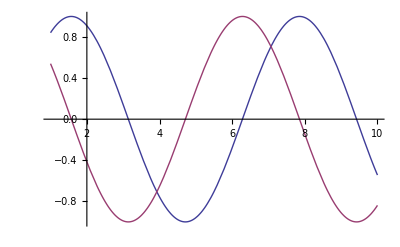

```mathematica
Plot[{Sin[x],Cos[x]},{x,1,10}]
```

```mathematica
(x+y) (x-y)^2/.{x->3,y->1-a}
```

(4-a) (2+a)^2

x=value	define a value for x that will always be used
x=.	remove any value defined for x

```mathematica
Expand[(1+x+3 y)^4]
```

1+4 x+6 x^2+4 x^3+x^4+12 y+36 x y+36 x^2 y+12 x^3 y+54 y^2+108 x y^2+54 x^2 y^2+108 y^3+108 x y^3+81 y^4

```mathematica
Factor[%]
```

(1+x+3 y)^4

Simplify[expr]	try to find the simplest form of expr by applying various standard algebraic transformations
FullSimplify[expr]	try to find the simplest form by applying a wide range of transformations

```mathematica
Integrate[1/(x^4-1),x]
```

-ArcTan[x]/2+1/4 Log[1-x]-1/4 Log[1+x]

```mathematica
D[%,x]
```

-1/(4 (1-x))-1/(4 (1+x))-1/(2 (1+x^2))

```mathematica
Simplify[%]
```

1/(-1+x^4)

```mathematica
D[f,x]    partial derivative
D[f,x,y,...]    multiple derivative
D[f,{x,n}]    n derivative
D[f,x,NonConstants->{v1,v2,...}]    with the taken to depend on x
```

```mathematica
D[f,{{x1,x2,...}}]    the gradient of a scalar function
D[f,{{x1,x2,...},2}]    the Hessian matrix for f
D[f,{{x1,x2,...},n}]    the n-order Taylor series coefficient
D[{f1,f2,...},{{x1,x2,...}}]    the Jacobian for a vector function f


Integrate[f,x]    the indefinite integral
Integrate[f,x,y]    the multiple integral
Integrate[f,{x,xmin,xmax}]    the definite integral
Integrate[f,{x,xmin,xmax},{y,ymin,ymax}]   the multiple integral
```

```mathematica
Simplify[D[{ArcTan[x],-ArcTan[1/x]},x]]
```

{1/(1+x^2),1/(1+x^2)}

```mathematica
DSolve[y'[x]+y[x]==1,y[x],x]
```

{{y[x]→1+ⅇ^-x C[1]}}

```mathematica
y[x]+2 y'[x]+y[0]/.%
```

{1+ⅇ^-x C[1]+y[0]+2 y'[x]}

```mathematica
DSolve[y'[x]+y[x]==1,y,x]
```

{{y→Function[{x},1+ⅇ^-x C[1]]}}

```mathematica
y[x]+2 y'[x]+y[0]/.%
```

{2+C[1]-ⅇ^-x C[1]}

```mathematica
y'[x]+y[x]==1/.%%
```

{True}

```mathematica
DSolve[{y[x]==-z'[x],z[x]==-y'[x]},{y,z},x]
```

{{y→Function[{x},1/2 ⅇ^-x (1+ⅇ^(2 x)) C[1]-1/2 ⅇ^-x (-1+ⅇ^(2 x)) C[2]],z→Function[{x},-1/2 ⅇ^-x (-1+ⅇ^(2 x)) C[1]+1/2 ⅇ^-x (1+ⅇ^(2 x)) C[2]]}}

```mathematica
DSolve[D[y[x1,x2],x1]+D[y[x1,x2],x2]==Exp[y[x1,x2]],y[x1,x2],{x1,x2}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x1,x2]→-Log[-x1-C[1][-x1+x2]]}}

## Plotting

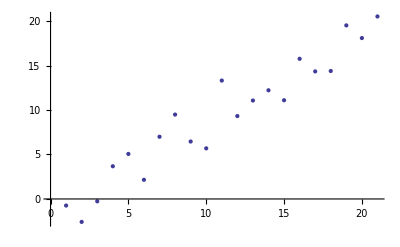

```mathematica
datapts=Table[x+RandomReal[{-4,4}],{x,0,20}];
ListPlot[datapts]
```

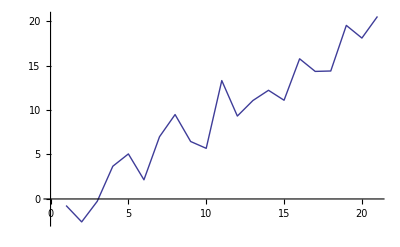

```mathematica
ListLinePlot[datapts]
```

```mathematica
Plot3D[Sin[x] Cos[y],{x,0,5},{y,1,10}]
```

-Graphics3D-

```mathematica
GraphicsGrid[{{Plot3D[Sin[x] Cos[y],{x,0,5},{y,1,10}],Plot3D[Sin[x]*Cos[y],{x,0,5},{y,1,10},ColorFunction->(Hue[#3]&),MeshFunctions->(#3&),Boxed->False,Axes->False]}}]
```

-Graphics-

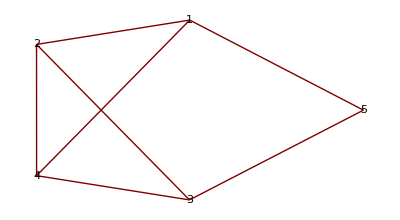

```mathematica
GraphPlot[{1->2,1->4,2->4,3->4,3->2,3->5,5->1},VertexLabeling->True]
```

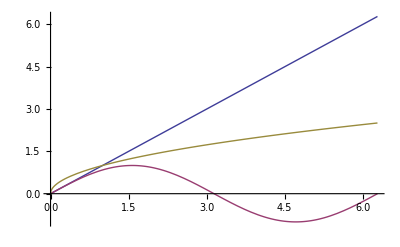

```mathematica
Plot[{x,Sin[x],Sqrt[x]},{x,0,2 Pi}]
```

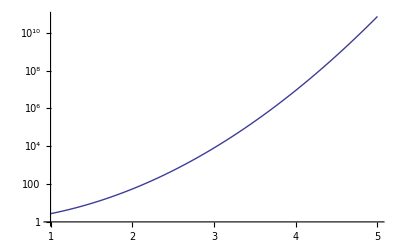

```mathematica
LogPlot[E^x^2,{x,1,5}]
```

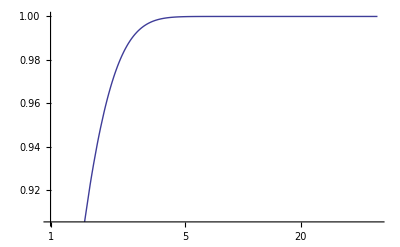

```mathematica
LogLinearPlot[Tanh[x],{x,1,50}]
```

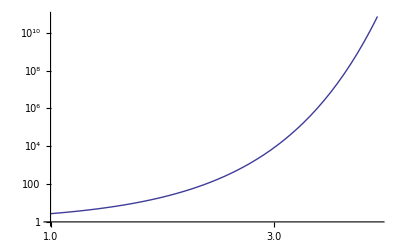

```mathematica
LogLogPlot[E^x^2,{x,1,5}]
```

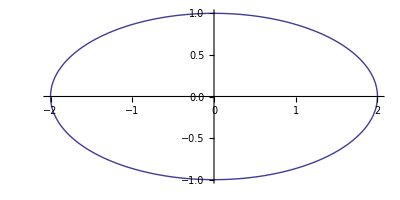

```mathematica
ParametricPlot[{2 Sin[t],Cos[t]},{t,0,2 Pi}]
```

```mathematica
ParametricPlot3D[{5 Cos[u],5 Sin[u],u+Sin[u]},{u,-2 Pi,2 Pi}]
```

-Graphics3D-

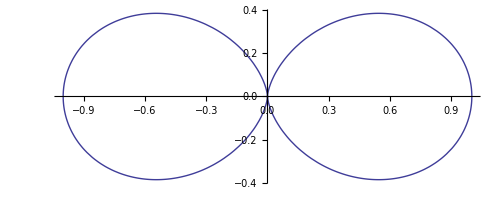

```mathematica
PolarPlot[Cos[t]^2,{t,0,2 Pi}]
```

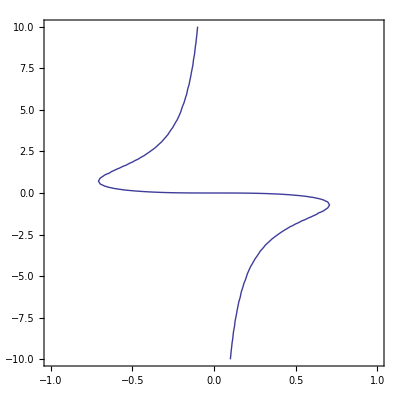

```mathematica
ContourPlot[x^3+x y^2+y==0,{x,-1,1},{y,-10,10}]
```

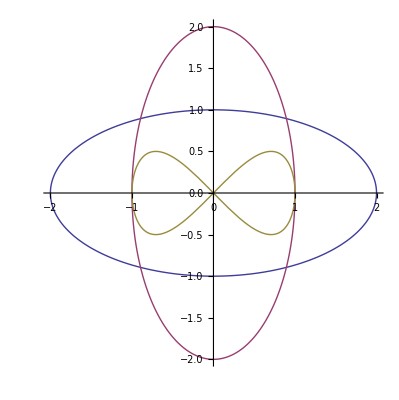

```mathematica
ParametricPlot[{{2 Sin[t],Cos[t]},{Sin[t],2 Cos[t]},{Sin[t],Sin[t] Cos[t]}},{t,0,2 Pi}]
```

```mathematica
ParametricPlot3D[{r Cos[t],r Sin[t],Log[r^(1/2)]},{r,0.1,1},{t,0,2 Pi}]
```

-Graphics3D-

```mathematica
Manipulate[Module[{sol=NDSolve[{y''[x]+Sin[y[x]]==0,y[0]==p[[1]],y'[0]==p[[2]]},y,{x,0,T}]},ParametricPlot[Evaluate[{y[x],y'[x]}/.sol],{x,0,T},PlotRange->{{-4,4},{-3,3}}]],{{p,{2,1}},Locator},{{T,10},0,100}]
```

```mathematica
wws = NDSolve[{D[u[t,x], t,t] == D[u[t,x], x,x] + (1 - u[t, x]^2) (1 + 2 u[t, x]), u[0, x] == E^-x^2, 
Derivative[1,0][u][0, x] == 0, u[t, -10] == u[t, 10]}, 
  u, {t, 0, 10}, {x, -10, 10}]
```

{{u→InterpolatingFunction[{{0.,10.},{-10.,10.}},<>]}}

```mathematica
Plot3D[u[t,x]/.wws,{t,0,10},{x,-10,10}]
```

-Graphics3D-

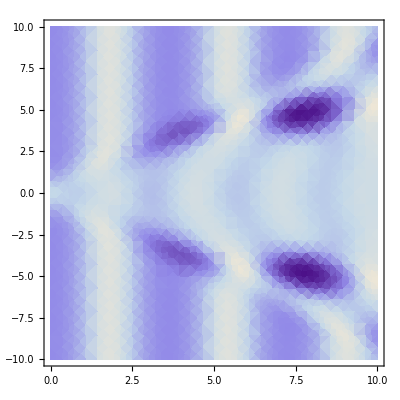

```mathematica
DensityPlot[u[t,x]/.wws,{t,0,10},{x,-10,10}]
```

## Manipulate

```mathematica
Manipulate[Plot[Sin[n x],{x,0,2 Pi}],{n,1,20,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},PlotRange->2],{n1,1,20},{n2,1,20}]
```

```mathematica
Manipulate[Expand[(α+β)^n],{n,1,300,1}]
```

```mathematica
Manipulate[Row[{n,"+",m,"=",n+m}],{n,a,10 a,a/12},{m,a,10 a,a/12}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},Filling->filling,PlotRange->2],{n1,1,20},{n2,1,20},{filling,{None,Axis,Top,Bottom}}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},Filling->filling,PlotRange->2],{n1,1,20},{n2,1,20},{filling,{None,Axis,Top,Bottom,Automatic,1,0.5,0,-0.5,-1},ControlType->Manipulator}]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{n1,1,4},{a1,0,1},{p1,0,2 Pi},{n2,1,4},{a2,0,1},{p2,0,2 Pi}]
```

```mathematica
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{n1,1,4},{{a1,1},0,1},{p1,0,2 Pi},{{n2,5/4},1,4},{{a2,1},0,1},{p2,0,2 Pi}]
```

```mathematica
Manipulate[Graphics[{PointSize[0.1],Point[pt]},PlotRange->1],{pt,{-1,-1},{1,1}}]
```

```mathematica
Manipulate[Graphics[{Line[Table[{{Cos[t],Sin[t]},pt},{t,2. Pi/n,2. Pi,2. Pi/n}]]},PlotRange->1],{{n,30},1,200,1},{pt,{-1,-1},{1,1}}]
```

```mathematica
Manipulate[Graphics[Line[Table[{{Sin[n+i],Cos[n+i]},{Sin[n+dn+i],Cos[n+dn+i]}},{i,0,di,di/l}]],PlotRange->1.1],{n,0,2 π},{dn,0,2 π},{di,1,2 π},{l,1,200},ControlPlacement->Left]
```

```mathematica
Manipulate[Plot3D[Sin[n x y],{x,0,3},{y,0,3}],{n,1,5}]
```

```mathematica
Manipulate[Graphics3D[{Sphere[{0,0,0},r1],Sphere[{c[[1]],c[[2]],0},r2]},PlotRange->2],{{r1,1},0,2},{{r2,1},0,2},{c,{-2,-2},{2,2}}]
```